## 1064 FORT, 780 Rydberg Beam Fits

Analysis of the FORT and 780 beams in the atom focal plane prior to the 2021 refactor.

## setup

```mathematica
imagedir=FileNameJoin[{NotebookDirectory[],"FORT_MOT_images_20210309\\"}];
AppendTo[$Path, FileNameJoin[{NotebookDirectory[],imagedir}]];
```

## 780

```mathematica
pixels780 = 11.9; (*pixels per microns in object plane, using Urban imaging camera with PointGrey CCD*)
```

```mathematica
img = ColorConvert[Import["780_xfocus_2021-03-09.png"],"grayscale"]
```

-Graphics-

```mathematica
(*data = ImageData[ImageRotate[img,-0.01]];*)
data = ImageData[img];
data = data-data[[50,50]];(*subtract off the background*)
data = Replace[data,_?Negative-> 0,{2}]; 
data = data/Max[data]; 
lenx = data//Length
leny= data[[1]]//Length
```

960

1280

```mathematica
(*Image[data[[860;;861, 1;; leny]]]*)
```

-Graphics-

```mathematica
(*Image[data[[869;;870,1;;leny]]]*)
```

-Graphics-

```mathematica
rotData = ImageData[ImageRotate[img,-0.01]];
Show[ImageData[rotData]]
```

0.0627451

#### 2D fit

This really doesn’t work well.

```mathematica
lenx
leny
```

960

1280

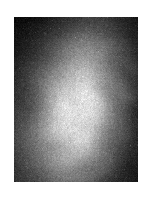

```mathematica
croppedData = data[[300;;500,550;;700]];
Show[Image[croppedData]]
```

```mathematica
croppedData//Dimensions
```

```mathematica
data3D = Flatten[MapIndexed[{#2[[1]],#2[[2]],#1}&,croppedData,{2}],1];
```

```mathematica
model = A  Exp[(-2(x-x0)^2)/σx^2] Exp[(-2(y-y0)^2)/σy^2] ;
fit =FindFit[data3D,model,{{x0,600},{y0,400},σx,σy,A},{x,y}]
```

FindFit::fmgz: Encountered a gradient that is effectively zero. The result returned may not be a minimum; it may be a maximum or a saddle point.

{x0→600.,y0→400.,σx→1.,σy→1.,A→1.}

```mathematica
ListPlot3D[data3D,Mesh->None]
```

-Graphics3D-

#### x waist fit

```mathematica
Show[Image[data],Graphics[{EdgeForm[Directive[Thin,Red]], Opacity[0],Rectangle[{1,540},{leny,550}]}],ImageSize->Medium]
```

-Graphics-

```mathematica
Image[data[[310;;540,1;;leny]]]
```

-Graphics-

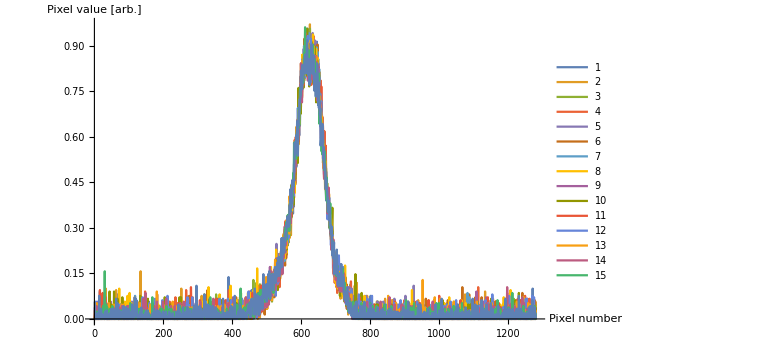

```mathematica
linedata[i_]:= Transpose@{Range[leny],data[[425+i;;426+i,1;;leny]][[1]]};
ListPlot[Evaluate[Table[linedata[j],{j,-10,5}]], Joined->True,AxesLabel-> {"Pixel number","Pixel value [arb.]"},LabelStyle-> Directive[Black, Medium],ImageSize-> Large,PlotRange->All,PlotLegends->Automatic]
```

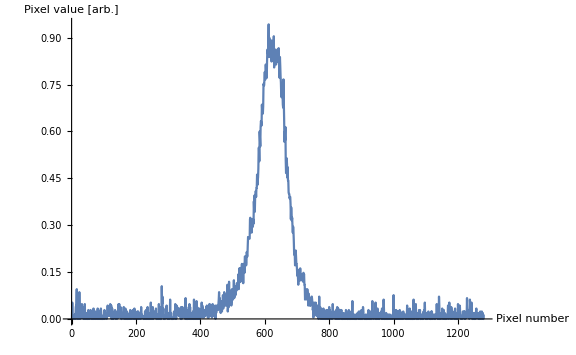

```mathematica
ListPlot[linedata[0], Joined->True,AxesLabel-> {"Pixel number","Pixel value [arb.]"},LabelStyle-> Directive[Black, Medium],ImageSize-> Large,PlotRange->All,PlotLegends->Automatic]
```

{μ→623.211,σ→89.7804,A→0.870207}

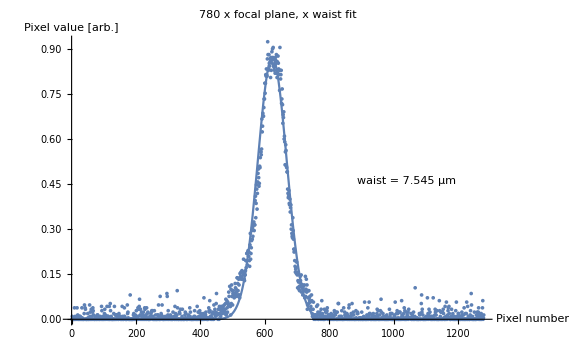

real space waist 7.545 [μm]

```mathematica
model = A  Exp[(-2(x-μ)^2)/σ^2];
fit =FindFit[linedata[0],model,{{μ,600},σ,A},x]
plt=Show[Plot[model/.fit,{x,0,leny},PlotRange->All,PlotLegends-> Placed[ToString[StringForm["waist = `` μm",NumberForm[Values[fit[[2]]]/pixels780,4]]],{0.8,0.5}]],ListPlot[linedata[-5]],AxesLabel-> {"Pixel number","Pixel value [arb.]"},ImageSize-> Large,
PlotLabel->"780 x focal plane, x waist fit",LabelStyle-> Directive[Black, FontSize-> 14],ImageSize-> Medium]
StringForm["real space waist `` [μm]",NumberForm[Values[fit[[2]]]/pixels780,4]]
```

```mathematica
Export[ToString[FileNameJoin[{imagedir,"780_xfocus_xwaist_20210310.png"}]],plt]
```

C:\Users\gothr\Documents\Graduate Research\Mathematica\lab_analysis\FORT_MOT_images_20210309\780_xfocus_xwaist_20210310.png

#### y waist fit

```mathematica
Show[Image[data],Graphics[{EdgeForm[Directive[Thin,Red]], Opacity[0],Rectangle[{620,1},{630,lenx}]}],ImageSize->Medium]
```

-Graphics-

```mathematica
Image[data[[1;;lenx,560;;700]]]
```

-Graphics-

```mathematica
linedata[i_]:= Transpose@{Range[lenx],Transpose[data[[1;;lenx,630+i;;630+i]]][[1]]};
(*linedata[i_]:= Transpose@{Range[leny],data[[545;;556,1;;leny]][[1]]};*)
(*ListPlot[Evaluate[Table[linedata[j],{j,-5,5}]], Joined->True,AxesLabel-> {"Pixel number","Pixel value [arb.]"},LabelStyle-> Directive[Black, Medium],ImageSize-> Large,PlotRange->All,PlotLegends->Automatic]*)
```

```mathematica
data[[545;;556,1;;leny]]//Dimensions
```

{12,1280}

```mathematica
linedata[-5]
```

{{1,0.00952381},{2,0.0190476},{3,0.00952381},{4,0.0714286},{5,0.00952381},{6,0.0285714},{7,0.0142857},{8,0.00952381},{9,0.00952381},{10,0.},{11,0.0047619},{12,0.},{13,0.},{14,0.00952381},{15,0.0238095},{16,0.},{17,0.0047619},{18,0.0142857},{19,0.00952381},{20,0.0047619},{21,0.0047619},{22,0.0238095},{23,0.0047619},{24,0.0190476},{25,0.00952381},{26,0.00952381},{27,0.0142857},{28,0.00952381},{29,0.0047619},{30,0.0142857},{31,0.0047619},{32,0.00952381},{33,0.},{34,0.00952381},{35,0.0142857},{36,0.0285714},{37,0.0142857},{38,0.0142857},{39,0.0142857},{40,0.0190476},{41,0.0285714},{42,0.00952381},{43,0.0047619},{44,0.0142857},{45,0.},{46,0.0142857},{47,0.0285714},{48,0.00952381},{49,0.},{50,0.0142857},{51,0.},{52,0.0142857},{53,0.0190476},{54,0.0142857},{55,0.0047619},{56,0.0190476},{57,0.0142857},{58,0.0571429},{59,0.},{60,0.00952381},{61,0.0047619},{62,0.0238095},{63,0.00952381},{64,0.0380952},{65,0.},{66,0.0142857},{67,0.0190476},{68,0.0380952},{69,0.0333333},{70,0.0190476},{71,0.},{72,0.0190476},{73,0.0047619},{74,0.},{75,0.0047619},{76,0.00952381},{77,0.0142857},{78,0.00952381},{79,0.0190476},{80,0.0380952},{81,0.0190476},{82,0.0047619},{83,0.},{84,0.00952381},{85,0.0047619},{86,0.0285714},{87,0.0142857},{88,0.0238095},{89,0.00952381},{90,0.},{91,0.0190476},{92,0.0190476},{93,0.0047619},{94,0.0238095},{95,0.0333333},{96,0.0285714},{97,0.0142857},{98,0.0285714},{99,0.},{100,0.0666667},{101,0.0142857},{102,0.0428571},{103,0.0190476},{104,0.0285714},{105,0.0333333},{106,0.0333333},{107,0.0190476},{108,0.0428571},{109,0.0380952},{110,0.0285714},{111,0.0238095},{112,0.0190476},{113,0.00952381},{114,0.0285714},{115,0.0190476},{116,0.0190476},{117,0.0238095},{118,0.0142857},{119,0.0142857},{120,0.},{121,0.0285714},{122,0.0238095},{123,0.0047619},{124,0.0333333},{125,0.0190476},{126,0.0380952},{127,0.0190476},{128,0.0285714},{129,0.0238095},{130,0.0285714},{131,0.0285714},{132,0.0285714},{133,0.0285714},{134,0.0238095},{135,0.0142857},{136,0.00952381},{137,0.0047619},{138,0.0047619},{139,0.0190476},{140,0.0285714},{141,0.0190476},{142,0.0428571},{143,0.00952381},{144,0.0238095},{145,0.0380952},{146,0.0428571},{147,0.0047619},{148,0.0333333},{149,0.0142857},{150,0.0142857},{151,0.0190476},{152,0.0238095},{153,0.00952381},{154,0.00952381},{155,0.0142857},{156,0.0380952},{157,0.0428571},{158,0.0285714},{159,0.00952381},{160,0.00952381},{161,0.0238095},{162,0.00952381},{163,0.0285714},{164,0.0142857},{165,0.0285714},{166,0.0285714},{167,0.0142857},{168,0.0285714},{169,0.0190476},{170,0.00952381},{171,0.0142857},{172,0.0142857},{173,0.0142857},{174,0.0047619},{175,0.},{176,0.0809524},{177,0.0047619},{178,0.},{179,0.00952381},{180,0.},{181,0.00952381},{182,0.0428571},{183,0.00952381},{184,0.0047619},{185,0.0333333},{186,0.0238095},{187,0.},{188,0.0285714},{189,0.0047619},{190,0.00952381},{191,0.0047619},{192,0.0190476},{193,0.00952381},{194,0.0047619},{195,0.},{196,0.00952381},{197,0.0047619},{198,0.00952381},{199,0.},{200,0.00952381},{201,0.0190476},{202,0.0190476},{203,0.0142857},{204,0.0142857},{205,0.0047619},{206,0.},{207,0.0285714},{208,0.},{209,0.0047619},{210,0.0190476},{211,0.},{212,0.0047619},{213,0.0285714},{214,0.052381},{215,0.0285714},{216,0.0333333},{217,0.00952381},{218,0.},{219,0.0142857},{220,0.0047619},{221,0.},{222,0.0333333},{223,0.0190476},{224,0.0380952},{225,0.00952381},{226,0.00952381},{227,0.0047619},{228,0.},{229,0.0047619},{230,0.},{231,0.},{232,0.00952381},{233,0.0190476},{234,0.0047619},{235,0.00952381},{236,0.0047619},{237,0.0190476},{238,0.0380952},{239,0.0142857},{240,0.0333333},{241,0.0238095},{242,0.0047619},{243,0.0380952},{244,0.00952381},{245,0.0190476},{246,0.0333333},{247,0.0142857},{248,0.0666667},{249,0.047619},{250,0.0190476},{251,0.0333333},{252,0.0380952},{253,0.0380952},{254,0.0666667},{255,0.0285714},{256,0.0285714},{257,0.0428571},{258,0.0571429},{259,0.047619},{260,0.0571429},{261,0.0714286},{262,0.052381},{263,0.047619},{264,0.0857143},{265,0.0571429},{266,0.0857143},{267,0.0761905},{268,0.047619},{269,0.133333},{270,0.0809524},{271,0.0809524},{272,0.114286},{273,0.1},{274,0.0666667},{275,0.119048},{276,0.138095},{277,0.1},{278,0.152381},{279,0.104762},{280,0.114286},{281,0.138095},{282,0.133333},{283,0.119048},{284,0.209524},{285,0.152381},{286,0.166667},{287,0.17619},{288,0.166667},{289,0.190476},{290,0.166667},{291,0.142857},{292,0.157143},{293,0.142857},{294,0.180952},{295,0.195238},{296,0.233333},{297,0.17619},{298,0.219048},{299,0.204762},{300,0.242857},{301,0.219048},{302,0.228571},{303,0.266667},{304,0.233333},{305,0.22381},{306,0.257143},{307,0.242857},{308,0.3},{309,0.271429},{310,0.242857},{311,0.280952},{312,0.304762},{313,0.280952},{314,0.3},{315,0.3},{316,0.280952},{317,0.304762},{318,0.347619},{319,0.366667},{320,0.338095},{321,0.347619},{322,0.338095},{323,0.371429},{324,0.42381},{325,0.433333},{326,0.409524},{327,0.438095},{328,0.395238},{329,0.447619},{330,0.42381},{331,0.442857},{332,0.461905},{333,0.457143},{334,0.466667},{335,0.519048},{336,0.538095},{337,0.566667},{338,0.552381},{339,0.533333},{340,0.509524},{341,0.538095},{342,0.533333},{343,0.538095},{344,0.542857},{345,0.547619},{346,0.57619},{347,0.585714},{348,0.571429},{349,0.609524},{350,0.604762},{351,0.585714},{352,0.595238},{353,0.633333},{354,0.657143},{355,0.590476},{356,0.628571},{357,0.661905},{358,0.661905},{359,0.628571},{360,0.680952},{361,0.709524},{362,0.652381},{363,0.680952},{364,0.733333},{365,0.695238},{366,0.738095},{367,0.709524},{368,0.780952},{369,0.761905},{370,0.752381},{371,0.747619},{372,0.752381},{373,0.690476},{374,0.757143},{375,0.785714},{376,0.728571},{377,0.747619},{378,0.790476},{379,0.780952},{380,0.833333},{381,0.771429},{382,0.771429},{383,0.842857},{384,0.890476},{385,0.871429},{386,0.82381},{387,0.87619},{388,0.838095},{389,0.861905},{390,0.838095},{391,0.914286},{392,0.909524},{393,0.819048},{394,0.8},{395,0.9},{396,0.857143},{397,0.890476},{398,0.880952},{399,0.814286},{400,0.766667},{401,0.852381},{402,0.8},{403,0.814286},{404,0.852381},{405,0.861905},{406,0.852381},{407,0.819048},{408,0.885714},{409,0.871429},{410,0.9},{411,0.885714},{412,0.857143},{413,0.928571},{414,0.861905},{415,0.852381},{416,0.971429},{417,0.957143},{418,0.852381},{419,0.914286},{420,0.871429},{421,0.890476},{422,0.87619},{423,0.904762},{424,0.885714},{425,0.880952},{426,0.866667},{427,0.87619},{428,0.87619},{429,0.838095},{430,0.795238},{431,0.880952},{432,0.842857},{433,0.828571},{434,0.895238},{435,0.919048},{436,0.885714},{437,0.871429},{438,0.947619},{439,0.952381},{440,0.795238},{441,0.847619},{442,0.857143},{443,0.890476},{444,0.890476},{445,0.904762},{446,0.838095},{447,0.828571},{448,0.804762},{449,0.847619},{450,0.780952},{451,0.828571},{452,0.761905},{453,0.795238},{454,0.871429},{455,0.819048},{456,0.752381},{457,0.771429},{458,0.728571},{459,0.733333},{460,0.842857},{461,0.719048},{462,0.747619},{463,0.742857},{464,0.742857},{465,0.719048},{466,0.685714},{467,0.695238},{468,0.680952},{469,0.638095},{470,0.67619},{471,0.652381},{472,0.628571},{473,0.642857},{474,0.647619},{475,0.62381},{476,0.666667},{477,0.628571},{478,0.557143},{479,0.57619},{480,0.628571},{481,0.585714},{482,0.557143},{483,0.533333},{484,0.580952},{485,0.57619},{486,0.585714},{487,0.547619},{488,0.528571},{489,0.490476},{490,0.490476},{491,0.509524},{492,0.466667},{493,0.514286},{494,0.447619},{495,0.457143},{496,0.42381},{497,0.404762},{498,0.438095},{499,0.504762},{500,0.442857},{501,0.433333},{502,0.390476},{503,0.490476},{504,0.390476},{505,0.390476},{506,0.419048},{507,0.380952},{508,0.37619},{509,0.347619},{510,0.371429},{511,0.333333},{512,0.371429},{513,0.342857},{514,0.280952},{515,0.342857},{516,0.333333},{517,0.271429},{518,0.280952},{519,0.295238},{520,0.266667},{521,0.295238},{522,0.266667},{523,0.266667},{524,0.238095},{525,0.266667},{526,0.27619},{527,0.271429},{528,0.233333},{529,0.204762},{530,0.261905},{531,0.204762},{532,0.190476},{533,0.195238},{534,0.190476},{535,0.228571},{536,0.180952},{537,0.185714},{538,0.152381},{539,0.180952},{540,0.166667},{541,0.133333},{542,0.161905},{543,0.142857},{544,0.104762},{545,0.114286},{546,0.12381},{547,0.109524},{548,0.114286},{549,0.104762},{550,0.0904762},{551,0.119048},{552,0.119048},{553,0.0809524},{554,0.0714286},{555,0.0809524},{556,0.0857143},{557,0.0714286},{558,0.114286},{559,0.0666667},{560,0.0761905},{561,0.0809524},{562,0.0761905},{563,0.0428571},{564,0.0714286},{565,0.0428571},{566,0.0380952},{567,0.0333333},{568,0.0904762},{569,0.0285714},{570,0.0857143},{571,0.109524},{572,0.0571429},{573,0.0428571},{574,0.0666667},{575,0.0380952},{576,0.0714286},{577,0.0666667},{578,0.0809524},{579,0.0380952},{580,0.0809524},{581,0.0380952},{582,0.0571429},{583,0.0190476},{584,0.0190476},{585,0.0333333},{586,0.0047619},{587,0.},{588,0.0238095},{589,0.0190476},{590,0.0190476},{591,0.00952381},{592,0.0285714},{593,0.0142857},{594,0.00952381},{595,0.0238095},{596,0.0428571},{597,0.},{598,0.0333333},{599,0.0190476},{600,0.0428571},{601,0.00952381},{602,0.0142857},{603,0.0428571},{604,0.0333333},{605,0.},{606,0.},{607,0.0190476},{608,0.0380952},{609,0.},{610,0.0619048},{611,0.0380952},{612,0.0190476},{613,0.},{614,0.0333333},{615,0.0619048},{616,0.0142857},{617,0.},{618,0.0380952},{619,0.0047619},{620,0.0047619},{621,0.0285714},{622,0.0238095},{623,0.},{624,0.},{625,0.0190476},{626,0.0142857},{627,0.},{628,0.0142857},{629,0.},{630,0.0285714},{631,0.047619},{632,0.0142857},{633,0.0190476},{634,0.0285714},{635,0.},{636,0.0333333},{637,0.0190476},{638,0.0238095},{639,0.},{640,0.0047619},{641,0.},{642,0.},{643,0.0238095},{644,0.0285714},{645,0.0190476},{646,0.},{647,0.0047619},{648,0.00952381},{649,0.},{650,0.0190476},{651,0.0047619},{652,0.0047619},{653,0.00952381},{654,0.},{655,0.},{656,0.0190476},{657,0.0142857},{658,0.0190476},{659,0.0238095},{660,0.0333333},{661,0.},{662,0.0333333},{663,0.},{664,0.},{665,0.},{666,0.00952381},{667,0.0190476},{668,0.052381},{669,0.0285714},{670,0.00952381},{671,0.0142857},{672,0.0238095},{673,0.00952381},{674,0.0333333},{675,0.0619048},{676,0.052381},{677,0.0190476},{678,0.00952381},{679,0.0285714},{680,0.0142857},{681,0.0047619},{682,0.0047619},{683,0.00952381},{684,0.0190476},{685,0.0238095},{686,0.0142857},{687,0.0238095},{688,0.0238095},{689,0.0333333},{690,0.0142857},{691,0.0047619},{692,0.00952381},{693,0.0190476},{694,0.00952381},{695,0.},{696,0.0047619},{697,0.},{698,0.},{699,0.0428571},{700,0.0285714},{701,0.00952381},{702,0.0619048},{703,0.0380952},{704,0.0238095},{705,0.0238095},{706,0.0428571},{707,0.0238095},{708,0.},{709,0.0238095},{710,0.0238095},{711,0.0142857},{712,0.0047619},{713,0.0190476},{714,0.00952381},{715,0.0333333},{716,0.},{717,0.052381},{718,0.0428571},{719,0.00952381},{720,0.},{721,0.0285714},{722,0.0285714},{723,0.},{724,0.052381},{725,0.0142857},{726,0.0047619},{727,0.0190476},{728,0.0047619},{729,0.0142857},{730,0.0333333},{731,0.0047619},{732,0.},{733,0.0047619},{734,0.00952381},{735,0.0047619},{736,0.0142857},{737,0.0142857},{738,0.0380952},{739,0.0238095},{740,0.0238095},{741,0.0047619},{742,0.00952381},{743,0.0285714},{744,0.0142857},{745,0.},{746,0.0333333},{747,0.00952381},{748,0.0047619},{749,0.0047619},{750,0.0380952},{751,0.0380952},{752,0.},{753,0.},{754,0.0238095},{755,0.0571429},{756,0.0238095},{757,0.00952381},{758,0.},{759,0.},{760,0.047619},{761,0.00952381},{762,0.},{763,0.},{764,0.0142857},{765,0.0238095},{766,0.},{767,0.0047619},{768,0.0047619},{769,0.},{770,0.0285714},{771,0.},{772,0.052381},{773,0.0142857},{774,0.0285714},{775,0.00952381},{776,0.0190476},{777,0.},{778,0.00952381},{779,0.0238095},{780,0.0619048},{781,0.00952381},{782,0.0047619},{783,0.},{784,0.0571429},{785,0.0238095},{786,0.},{787,0.0285714},{788,0.},{789,0.0142857},{790,0.0333333},{791,0.00952381},{792,0.00952381},{793,0.0238095},{794,0.0190476},{795,0.0047619},{796,0.0714286},{797,0.0238095},{798,0.047619},{799,0.0047619},{800,0.0190476},{801,0.0380952},{802,0.0380952},{803,0.},{804,0.0238095},{805,0.0285714},{806,0.0571429},{807,0.0047619},{808,0.00952381},{809,0.},{810,0.0142857},{811,0.},{812,0.},{813,0.0380952},{814,0.0904762},{815,0.0238095},{816,0.00952381},{817,0.},{818,0.},{819,0.},{820,0.},{821,0.0619048},{822,0.},{823,0.0047619},{824,0.0380952},{825,0.},{826,0.00952381},{827,0.00952381},{828,0.0142857},{829,0.0142857},{830,0.00952381},{831,0.00952381},{832,0.},{833,0.0238095},{834,0.0047619},{835,0.0190476},{836,0.},{837,0.0142857},{838,0.0190476},{839,0.0714286},{840,0.00952381},{841,0.},{842,0.0190476},{843,0.},{844,0.0285714},{845,0.0380952},{846,0.052381},{847,0.},{848,0.0666667},{849,0.},{850,0.},{851,0.0190476},{852,0.0047619},{853,0.0047619},{854,0.12381},{855,0.},{856,0.0761905},{857,0.0190476},{858,0.},{859,0.0047619},{860,0.0142857},{861,0.0142857},{862,0.00952381},{863,0.0142857},{864,0.},{865,0.},{866,0.},{867,0.00952381},{868,0.},{869,0.0285714},{870,0.00952381},{871,0.},{872,0.00952381},{873,0.},{874,0.0380952},{875,0.0238095},{876,0.},{877,0.0047619},{878,0.0190476},{879,0.0190476},{880,0.0571429},{881,0.0428571},{882,0.00952381},{883,0.0142857},{884,0.0047619},{885,0.0190476},{886,0.0047619},{887,0.0142857},{888,0.0190476},{889,0.},{890,0.0285714},{891,0.0047619},{892,0.},{893,0.},{894,0.00952381},{895,0.},{896,0.},{897,0.0142857},{898,0.00952381},{899,0.0142857},{900,0.0809524},{901,0.0047619},{902,0.},{903,0.0142857},{904,0.0428571},{905,0.0428571},{906,0.0333333},{907,0.},{908,0.},{909,0.0047619},{910,0.0190476},{911,0.0047619},{912,0.},{913,0.0142857},{914,0.0142857},{915,0.0238095},{916,0.0238095},{917,0.0238095},{918,0.0238095},{919,0.0047619},{920,0.00952381},{921,0.0142857},{922,0.00952381},{923,0.0285714},{924,0.},{925,0.0190476},{926,0.},{927,0.0285714},{928,0.0333333},{929,0.0428571},{930,0.},{931,0.0142857},{932,0.},{933,0.00952381},{934,0.0380952},{935,0.0047619},{936,0.0333333},{937,0.0238095},{938,0.0904762},{939,0.00952381},{940,0.},{941,0.},{942,0.0380952},{943,0.},{944,0.0238095},{945,0.00952381},{946,0.0190476},{947,0.0238095},{948,0.0238095},{949,0.0142857},{950,0.052381},{951,0.0238095},{952,0.0238095},{953,0.},{954,0.0047619},{955,0.},{956,0.00952381},{957,0.00952381},{958,0.},{959,0.},{960,0.00952381}}

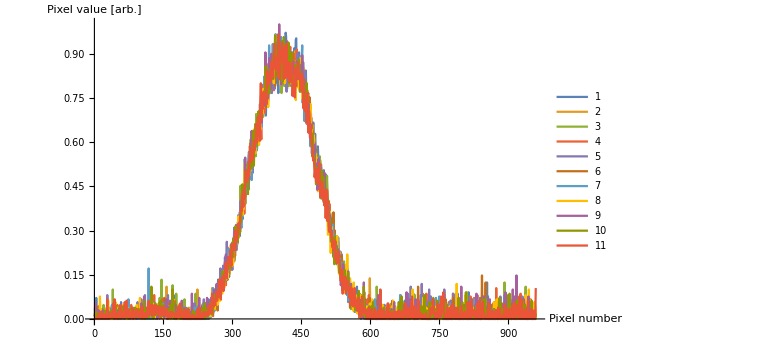

```mathematica
ListPlot[Evaluate[Table[linedata[j],{j,-5,5}]], Joined->True,AxesLabel-> {"Pixel number","Pixel value [arb.]"},LabelStyle-> Directive[Black, Medium],ImageSize-> Large,PlotRange->All,PlotLegends->Automatic]
```

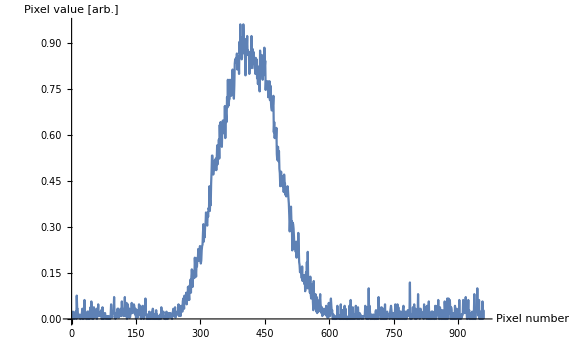

```mathematica
ListPlot[linedata[2], Joined->True,AxesLabel-> {"Pixel number","Pixel value [arb.]"},LabelStyle-> Directive[Black, Medium],ImageSize-> Large,PlotRange->All,PlotLegends->Automatic]
```

{μ→412.158,σ→137.062,A→0.898258}

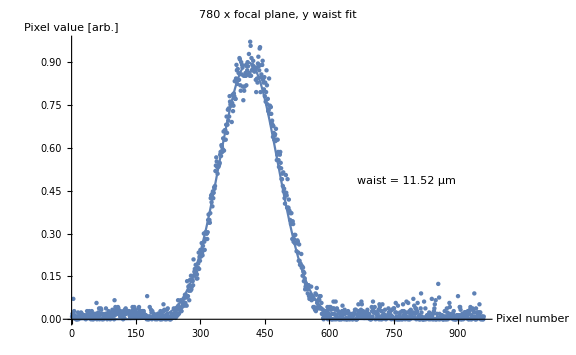

real space waist 11.52 [μm]

```mathematica
model = A  Exp[(-2(x-μ)^2)/σ^2];
fit =FindFit[linedata[2],model,{{μ,400},σ,A},x]
plt=Show[Plot[model/.fit,{x,0,lenx},PlotRange->All,PlotLegends-> Placed[ToString[StringForm["waist = `` μm",NumberForm[Values[fit[[2]]]/pixels780,4]]],{0.8,0.5}]],ListPlot[linedata[-5]],AxesLabel-> {"Pixel number","Pixel value [arb.]"},ImageSize-> Large,
PlotLabel->"780 x focal plane, y waist fit",LabelStyle-> Directive[Black, FontSize-> 14],ImageSize-> Medium]
StringForm["real space waist `` [μm]",NumberForm[Values[fit[[2]]]/pixels780,4]]
```

```mathematica
(*Export[ToString[FileNameJoin[{imagedir,"780_xfocus_ywaist_20210310.png"}]],plt]*)
```

C:\Users\gothr\Documents\Graduate Research\Mathematica\lab_analysis\FORT_MOT_images_20210309\780_xfocus_ywaist_20210310.png

show both slices:

```mathematica
beamslices=Show[Image[data],Graphics[{EdgeForm[Directive[Thin,Red]], Opacity[0],Rectangle[{620,1},{630,lenx}]}],Graphics[{EdgeForm[Directive[Thin,Red]], Opacity[0],Rectangle[{1,540},{leny,550}]}],ImageSize->Medium]
```

-Graphics-

```mathematica
Export[ToString[FileNameJoin[{imagedir,"780_beamslices_20210310.png"}]],beamslices]
```

C:\Users\gothr\Documents\Graduate Research\Mathematica\lab_analysis\FORT_MOT_images_20210309\780_beamslices_20210310.png

```mathematica
ToString[FileNameJoin[{imagedir,"780_beamslices_20210310.png"}]]
```

FileNameJoin[{FileNameJoin[{NotebookDirectory, FORT_MOT_images_20210309\}], 780_beamslices_20210310.png}]

## 1064

```mathematica
pixels1064 = 12.5; (*pixels per microns in object plane, using Urban imaging camera with PointGrey CCD*)
```

```mathematica
img = ColorConvert[Import["FORT_focus-2021-03-09.png"],"grayscale"]
```

-Graphics-

```mathematica
(*data = ImageData[ImageRotate[img,-0.01]];*)
data = ImageData[img];
data = data-data[[50,50]];(*subtract off the background*)
data = Replace[data,_?Negative-> 0,{2}]; 
data = data/Max[data]; 
lenx = data//Length
leny= data[[1]]//Length
```

960

1280

```mathematica
(*Image[data[[860;;861, 1;; leny]]]*)
```

-Graphics-

```mathematica
(*Image[data[[869;;870,1;;leny]]]*)
```

-Graphics-

```mathematica
rotData = ImageData[ImageRotate[img,-0.01]];
Show[ImageData[rotData]]
```

0.0627451

#### x waist fit

```mathematica
Show[Image[data],Graphics[{EdgeForm[Directive[Thin,Red]], Opacity[0],Rectangle[{1,515},{leny,525}]}],ImageSize->Medium]
```

-Graphics-

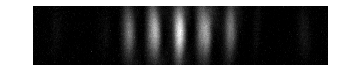

```mathematica
Show[Image[data[[420;;470,1;;leny]]],ImageSize->Medium]
```

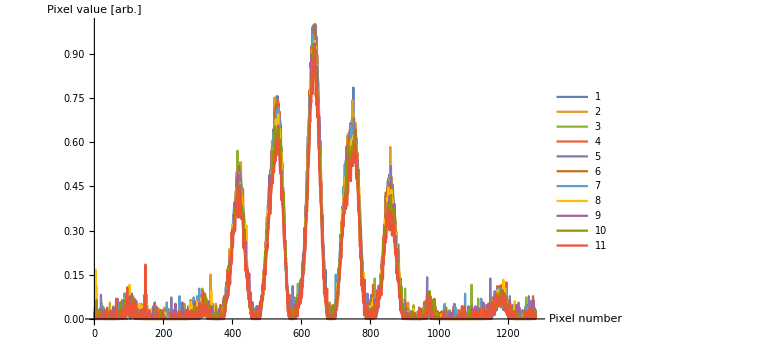

```mathematica
xstart=445;
linedata[i_]:= Transpose@{Range[leny],data[[xstart+i;;xstart+1+i,1;;leny]][[1]]};
ListPlot[Evaluate[Table[linedata[j],{j,-5,5}]], Joined->True,AxesLabel-> {"Pixel number","Pixel value [arb.]"},LabelStyle-> Directive[Black, Medium],ImageSize-> Large,PlotRange->All,PlotLegends->Automatic]
```

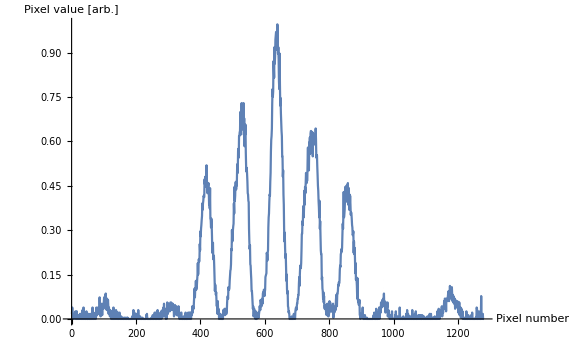

```mathematica
ListPlot[linedata[0], Joined->True,AxesLabel-> {"Pixel number","Pixel value [arb.]"},LabelStyle-> Directive[Black, Medium],ImageSize-> Large,PlotRange->All,PlotLegends->Automatic]
```

{μ0→417.416,μ1→526.848,μ2→636.535,μ3→745.374,μ4→857.4,σ0→34.4767,σ1→38.6616,σ2→33.1542,a→0.468928,b→0.686145,c→0.961321}

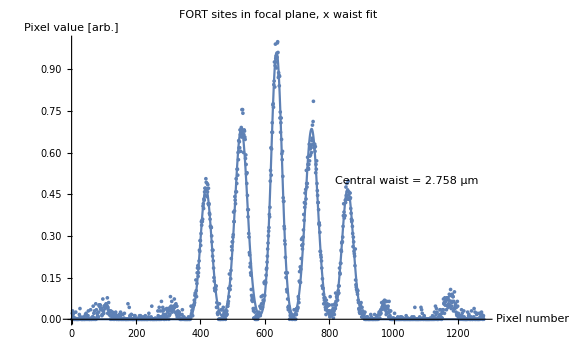

real space waist 2.758 [μm]

```mathematica
model = a  (Exp[(-2(x-μ0)^2)/σ0^2]+Exp[(-2(x-μ4)^2)/σ0^2])+b(Exp[(-2(x-μ1)^2)/σ1^2]+Exp[(-2(x-μ3)^2)/σ1^2])+c Exp[(-2(x-μ2)^2)/σ2^2];
fit =FindFit[linedata[-5],model,{{μ0,400},{μ1,525},{μ2,630},{μ3,750},{μ4,850},σ0,σ1,σ2,a,b,c},x]
plt=Show[Plot[model/.fit,{x,0,leny},PlotRange->All,PlotLegends-> Placed[ToString[StringForm["Central waist = `` μm",NumberForm[Values[fit[[6]]]/pixels1064,4]]],{0.8,0.5}]],ListPlot[linedata[-5]],AxesLabel-> {"Pixel number","Pixel value [arb.]"},ImageSize-> Large,
PlotLabel->"FORT sites in focal plane, x waist fit",LabelStyle-> Directive[Black, FontSize-> 14],ImageSize-> Medium]
StringForm["real space waist `` [μm]",NumberForm[Values[fit[[6]]]/pixels1064,4]]
```

```mathematica
(Values[fit[[1]]]- Values[fit[[2]]])/pixels1064
```

-8.75456

```mathematica
Values[fit[[3]]]
```

636.535

```mathematica
Values[fit[[2]]]
```

526.99

```mathematica
(*Export[ToString[FileNameJoin[{imagedir,"1064_FORT_fit_20210310.png"}]],plt]*)
```

C:\Users\gothr\Documents\Graduate Research\Mathematica\lab_analysis\FORT_MOT_images_20210309\1064_FORT_fit_20210310.png

#### y waist fit

```mathematica
Show[Image[data],Graphics[{EdgeForm[Directive[Thin,Red]], Opacity[0],Rectangle[{620,1},{630,lenx}]}],ImageSize->Medium]
```

-Graphics-

```mathematica
linedata[i_]:= Transpose@{Range[lenx],Transpose[data[[1;;lenx,625+i;;626+i]]][[1]]};
(*linedata[i_]:= Transpose@{Range[leny],data[[545;;556,1;;leny]][[1]]};*)
(*ListPlot[Evaluate[Table[linedata[j],{j,-5,5}]], Joined->True,AxesLabel-> {"Pixel number","Pixel value [arb.]"},LabelStyle-> Directive[Black, Medium],ImageSize-> Large,PlotRange->All,PlotLegends->Automatic]*)
```

```mathematica
Transpose[data[[1;;lenx,625;;630]]]//Dimensions
```

{6,960}

```mathematica
data[[545;;556,1;;leny]]//Dimensions
```

{12,1280}

```mathematica
linedata[-5]
```

{{1,0.00952381},{2,0.0190476},{3,0.00952381},{4,0.0714286},{5,0.00952381},{6,0.0285714},{7,0.0142857},{8,0.00952381},{9,0.00952381},{10,0.},{11,0.0047619},{12,0.},{13,0.},{14,0.00952381},{15,0.0238095},{16,0.},{17,0.0047619},{18,0.0142857},{19,0.00952381},{20,0.0047619},{21,0.0047619},{22,0.0238095},{23,0.0047619},{24,0.0190476},{25,0.00952381},{26,0.00952381},{27,0.0142857},{28,0.00952381},{29,0.0047619},{30,0.0142857},{31,0.0047619},{32,0.00952381},{33,0.},{34,0.00952381},{35,0.0142857},{36,0.0285714},{37,0.0142857},{38,0.0142857},{39,0.0142857},{40,0.0190476},{41,0.0285714},{42,0.00952381},{43,0.0047619},{44,0.0142857},{45,0.},{46,0.0142857},{47,0.0285714},{48,0.00952381},{49,0.},{50,0.0142857},{51,0.},{52,0.0142857},{53,0.0190476},{54,0.0142857},{55,0.0047619},{56,0.0190476},{57,0.0142857},{58,0.0571429},{59,0.},{60,0.00952381},{61,0.0047619},{62,0.0238095},{63,0.00952381},{64,0.0380952},{65,0.},{66,0.0142857},{67,0.0190476},{68,0.0380952},{69,0.0333333},{70,0.0190476},{71,0.},{72,0.0190476},{73,0.0047619},{74,0.},{75,0.0047619},{76,0.00952381},{77,0.0142857},{78,0.00952381},{79,0.0190476},{80,0.0380952},{81,0.0190476},{82,0.0047619},{83,0.},{84,0.00952381},{85,0.0047619},{86,0.0285714},{87,0.0142857},{88,0.0238095},{89,0.00952381},{90,0.},{91,0.0190476},{92,0.0190476},{93,0.0047619},{94,0.0238095},{95,0.0333333},{96,0.0285714},{97,0.0142857},{98,0.0285714},{99,0.},{100,0.0666667},{101,0.0142857},{102,0.0428571},{103,0.0190476},{104,0.0285714},{105,0.0333333},{106,0.0333333},{107,0.0190476},{108,0.0428571},{109,0.0380952},{110,0.0285714},{111,0.0238095},{112,0.0190476},{113,0.00952381},{114,0.0285714},{115,0.0190476},{116,0.0190476},{117,0.0238095},{118,0.0142857},{119,0.0142857},{120,0.},{121,0.0285714},{122,0.0238095},{123,0.0047619},{124,0.0333333},{125,0.0190476},{126,0.0380952},{127,0.0190476},{128,0.0285714},{129,0.0238095},{130,0.0285714},{131,0.0285714},{132,0.0285714},{133,0.0285714},{134,0.0238095},{135,0.0142857},{136,0.00952381},{137,0.0047619},{138,0.0047619},{139,0.0190476},{140,0.0285714},{141,0.0190476},{142,0.0428571},{143,0.00952381},{144,0.0238095},{145,0.0380952},{146,0.0428571},{147,0.0047619},{148,0.0333333},{149,0.0142857},{150,0.0142857},{151,0.0190476},{152,0.0238095},{153,0.00952381},{154,0.00952381},{155,0.0142857},{156,0.0380952},{157,0.0428571},{158,0.0285714},{159,0.00952381},{160,0.00952381},{161,0.0238095},{162,0.00952381},{163,0.0285714},{164,0.0142857},{165,0.0285714},{166,0.0285714},{167,0.0142857},{168,0.0285714},{169,0.0190476},{170,0.00952381},{171,0.0142857},{172,0.0142857},{173,0.0142857},{174,0.0047619},{175,0.},{176,0.0809524},{177,0.0047619},{178,0.},{179,0.00952381},{180,0.},{181,0.00952381},{182,0.0428571},{183,0.00952381},{184,0.0047619},{185,0.0333333},{186,0.0238095},{187,0.},{188,0.0285714},{189,0.0047619},{190,0.00952381},{191,0.0047619},{192,0.0190476},{193,0.00952381},{194,0.0047619},{195,0.},{196,0.00952381},{197,0.0047619},{198,0.00952381},{199,0.},{200,0.00952381},{201,0.0190476},{202,0.0190476},{203,0.0142857},{204,0.0142857},{205,0.0047619},{206,0.},{207,0.0285714},{208,0.},{209,0.0047619},{210,0.0190476},{211,0.},{212,0.0047619},{213,0.0285714},{214,0.052381},{215,0.0285714},{216,0.0333333},{217,0.00952381},{218,0.},{219,0.0142857},{220,0.0047619},{221,0.},{222,0.0333333},{223,0.0190476},{224,0.0380952},{225,0.00952381},{226,0.00952381},{227,0.0047619},{228,0.},{229,0.0047619},{230,0.},{231,0.},{232,0.00952381},{233,0.0190476},{234,0.0047619},{235,0.00952381},{236,0.0047619},{237,0.0190476},{238,0.0380952},{239,0.0142857},{240,0.0333333},{241,0.0238095},{242,0.0047619},{243,0.0380952},{244,0.00952381},{245,0.0190476},{246,0.0333333},{247,0.0142857},{248,0.0666667},{249,0.047619},{250,0.0190476},{251,0.0333333},{252,0.0380952},{253,0.0380952},{254,0.0666667},{255,0.0285714},{256,0.0285714},{257,0.0428571},{258,0.0571429},{259,0.047619},{260,0.0571429},{261,0.0714286},{262,0.052381},{263,0.047619},{264,0.0857143},{265,0.0571429},{266,0.0857143},{267,0.0761905},{268,0.047619},{269,0.133333},{270,0.0809524},{271,0.0809524},{272,0.114286},{273,0.1},{274,0.0666667},{275,0.119048},{276,0.138095},{277,0.1},{278,0.152381},{279,0.104762},{280,0.114286},{281,0.138095},{282,0.133333},{283,0.119048},{284,0.209524},{285,0.152381},{286,0.166667},{287,0.17619},{288,0.166667},{289,0.190476},{290,0.166667},{291,0.142857},{292,0.157143},{293,0.142857},{294,0.180952},{295,0.195238},{296,0.233333},{297,0.17619},{298,0.219048},{299,0.204762},{300,0.242857},{301,0.219048},{302,0.228571},{303,0.266667},{304,0.233333},{305,0.22381},{306,0.257143},{307,0.242857},{308,0.3},{309,0.271429},{310,0.242857},{311,0.280952},{312,0.304762},{313,0.280952},{314,0.3},{315,0.3},{316,0.280952},{317,0.304762},{318,0.347619},{319,0.366667},{320,0.338095},{321,0.347619},{322,0.338095},{323,0.371429},{324,0.42381},{325,0.433333},{326,0.409524},{327,0.438095},{328,0.395238},{329,0.447619},{330,0.42381},{331,0.442857},{332,0.461905},{333,0.457143},{334,0.466667},{335,0.519048},{336,0.538095},{337,0.566667},{338,0.552381},{339,0.533333},{340,0.509524},{341,0.538095},{342,0.533333},{343,0.538095},{344,0.542857},{345,0.547619},{346,0.57619},{347,0.585714},{348,0.571429},{349,0.609524},{350,0.604762},{351,0.585714},{352,0.595238},{353,0.633333},{354,0.657143},{355,0.590476},{356,0.628571},{357,0.661905},{358,0.661905},{359,0.628571},{360,0.680952},{361,0.709524},{362,0.652381},{363,0.680952},{364,0.733333},{365,0.695238},{366,0.738095},{367,0.709524},{368,0.780952},{369,0.761905},{370,0.752381},{371,0.747619},{372,0.752381},{373,0.690476},{374,0.757143},{375,0.785714},{376,0.728571},{377,0.747619},{378,0.790476},{379,0.780952},{380,0.833333},{381,0.771429},{382,0.771429},{383,0.842857},{384,0.890476},{385,0.871429},{386,0.82381},{387,0.87619},{388,0.838095},{389,0.861905},{390,0.838095},{391,0.914286},{392,0.909524},{393,0.819048},{394,0.8},{395,0.9},{396,0.857143},{397,0.890476},{398,0.880952},{399,0.814286},{400,0.766667},{401,0.852381},{402,0.8},{403,0.814286},{404,0.852381},{405,0.861905},{406,0.852381},{407,0.819048},{408,0.885714},{409,0.871429},{410,0.9},{411,0.885714},{412,0.857143},{413,0.928571},{414,0.861905},{415,0.852381},{416,0.971429},{417,0.957143},{418,0.852381},{419,0.914286},{420,0.871429},{421,0.890476},{422,0.87619},{423,0.904762},{424,0.885714},{425,0.880952},{426,0.866667},{427,0.87619},{428,0.87619},{429,0.838095},{430,0.795238},{431,0.880952},{432,0.842857},{433,0.828571},{434,0.895238},{435,0.919048},{436,0.885714},{437,0.871429},{438,0.947619},{439,0.952381},{440,0.795238},{441,0.847619},{442,0.857143},{443,0.890476},{444,0.890476},{445,0.904762},{446,0.838095},{447,0.828571},{448,0.804762},{449,0.847619},{450,0.780952},{451,0.828571},{452,0.761905},{453,0.795238},{454,0.871429},{455,0.819048},{456,0.752381},{457,0.771429},{458,0.728571},{459,0.733333},{460,0.842857},{461,0.719048},{462,0.747619},{463,0.742857},{464,0.742857},{465,0.719048},{466,0.685714},{467,0.695238},{468,0.680952},{469,0.638095},{470,0.67619},{471,0.652381},{472,0.628571},{473,0.642857},{474,0.647619},{475,0.62381},{476,0.666667},{477,0.628571},{478,0.557143},{479,0.57619},{480,0.628571},{481,0.585714},{482,0.557143},{483,0.533333},{484,0.580952},{485,0.57619},{486,0.585714},{487,0.547619},{488,0.528571},{489,0.490476},{490,0.490476},{491,0.509524},{492,0.466667},{493,0.514286},{494,0.447619},{495,0.457143},{496,0.42381},{497,0.404762},{498,0.438095},{499,0.504762},{500,0.442857},{501,0.433333},{502,0.390476},{503,0.490476},{504,0.390476},{505,0.390476},{506,0.419048},{507,0.380952},{508,0.37619},{509,0.347619},{510,0.371429},{511,0.333333},{512,0.371429},{513,0.342857},{514,0.280952},{515,0.342857},{516,0.333333},{517,0.271429},{518,0.280952},{519,0.295238},{520,0.266667},{521,0.295238},{522,0.266667},{523,0.266667},{524,0.238095},{525,0.266667},{526,0.27619},{527,0.271429},{528,0.233333},{529,0.204762},{530,0.261905},{531,0.204762},{532,0.190476},{533,0.195238},{534,0.190476},{535,0.228571},{536,0.180952},{537,0.185714},{538,0.152381},{539,0.180952},{540,0.166667},{541,0.133333},{542,0.161905},{543,0.142857},{544,0.104762},{545,0.114286},{546,0.12381},{547,0.109524},{548,0.114286},{549,0.104762},{550,0.0904762},{551,0.119048},{552,0.119048},{553,0.0809524},{554,0.0714286},{555,0.0809524},{556,0.0857143},{557,0.0714286},{558,0.114286},{559,0.0666667},{560,0.0761905},{561,0.0809524},{562,0.0761905},{563,0.0428571},{564,0.0714286},{565,0.0428571},{566,0.0380952},{567,0.0333333},{568,0.0904762},{569,0.0285714},{570,0.0857143},{571,0.109524},{572,0.0571429},{573,0.0428571},{574,0.0666667},{575,0.0380952},{576,0.0714286},{577,0.0666667},{578,0.0809524},{579,0.0380952},{580,0.0809524},{581,0.0380952},{582,0.0571429},{583,0.0190476},{584,0.0190476},{585,0.0333333},{586,0.0047619},{587,0.},{588,0.0238095},{589,0.0190476},{590,0.0190476},{591,0.00952381},{592,0.0285714},{593,0.0142857},{594,0.00952381},{595,0.0238095},{596,0.0428571},{597,0.},{598,0.0333333},{599,0.0190476},{600,0.0428571},{601,0.00952381},{602,0.0142857},{603,0.0428571},{604,0.0333333},{605,0.},{606,0.},{607,0.0190476},{608,0.0380952},{609,0.},{610,0.0619048},{611,0.0380952},{612,0.0190476},{613,0.},{614,0.0333333},{615,0.0619048},{616,0.0142857},{617,0.},{618,0.0380952},{619,0.0047619},{620,0.0047619},{621,0.0285714},{622,0.0238095},{623,0.},{624,0.},{625,0.0190476},{626,0.0142857},{627,0.},{628,0.0142857},{629,0.},{630,0.0285714},{631,0.047619},{632,0.0142857},{633,0.0190476},{634,0.0285714},{635,0.},{636,0.0333333},{637,0.0190476},{638,0.0238095},{639,0.},{640,0.0047619},{641,0.},{642,0.},{643,0.0238095},{644,0.0285714},{645,0.0190476},{646,0.},{647,0.0047619},{648,0.00952381},{649,0.},{650,0.0190476},{651,0.0047619},{652,0.0047619},{653,0.00952381},{654,0.},{655,0.},{656,0.0190476},{657,0.0142857},{658,0.0190476},{659,0.0238095},{660,0.0333333},{661,0.},{662,0.0333333},{663,0.},{664,0.},{665,0.},{666,0.00952381},{667,0.0190476},{668,0.052381},{669,0.0285714},{670,0.00952381},{671,0.0142857},{672,0.0238095},{673,0.00952381},{674,0.0333333},{675,0.0619048},{676,0.052381},{677,0.0190476},{678,0.00952381},{679,0.0285714},{680,0.0142857},{681,0.0047619},{682,0.0047619},{683,0.00952381},{684,0.0190476},{685,0.0238095},{686,0.0142857},{687,0.0238095},{688,0.0238095},{689,0.0333333},{690,0.0142857},{691,0.0047619},{692,0.00952381},{693,0.0190476},{694,0.00952381},{695,0.},{696,0.0047619},{697,0.},{698,0.},{699,0.0428571},{700,0.0285714},{701,0.00952381},{702,0.0619048},{703,0.0380952},{704,0.0238095},{705,0.0238095},{706,0.0428571},{707,0.0238095},{708,0.},{709,0.0238095},{710,0.0238095},{711,0.0142857},{712,0.0047619},{713,0.0190476},{714,0.00952381},{715,0.0333333},{716,0.},{717,0.052381},{718,0.0428571},{719,0.00952381},{720,0.},{721,0.0285714},{722,0.0285714},{723,0.},{724,0.052381},{725,0.0142857},{726,0.0047619},{727,0.0190476},{728,0.0047619},{729,0.0142857},{730,0.0333333},{731,0.0047619},{732,0.},{733,0.0047619},{734,0.00952381},{735,0.0047619},{736,0.0142857},{737,0.0142857},{738,0.0380952},{739,0.0238095},{740,0.0238095},{741,0.0047619},{742,0.00952381},{743,0.0285714},{744,0.0142857},{745,0.},{746,0.0333333},{747,0.00952381},{748,0.0047619},{749,0.0047619},{750,0.0380952},{751,0.0380952},{752,0.},{753,0.},{754,0.0238095},{755,0.0571429},{756,0.0238095},{757,0.00952381},{758,0.},{759,0.},{760,0.047619},{761,0.00952381},{762,0.},{763,0.},{764,0.0142857},{765,0.0238095},{766,0.},{767,0.0047619},{768,0.0047619},{769,0.},{770,0.0285714},{771,0.},{772,0.052381},{773,0.0142857},{774,0.0285714},{775,0.00952381},{776,0.0190476},{777,0.},{778,0.00952381},{779,0.0238095},{780,0.0619048},{781,0.00952381},{782,0.0047619},{783,0.},{784,0.0571429},{785,0.0238095},{786,0.},{787,0.0285714},{788,0.},{789,0.0142857},{790,0.0333333},{791,0.00952381},{792,0.00952381},{793,0.0238095},{794,0.0190476},{795,0.0047619},{796,0.0714286},{797,0.0238095},{798,0.047619},{799,0.0047619},{800,0.0190476},{801,0.0380952},{802,0.0380952},{803,0.},{804,0.0238095},{805,0.0285714},{806,0.0571429},{807,0.0047619},{808,0.00952381},{809,0.},{810,0.0142857},{811,0.},{812,0.},{813,0.0380952},{814,0.0904762},{815,0.0238095},{816,0.00952381},{817,0.},{818,0.},{819,0.},{820,0.},{821,0.0619048},{822,0.},{823,0.0047619},{824,0.0380952},{825,0.},{826,0.00952381},{827,0.00952381},{828,0.0142857},{829,0.0142857},{830,0.00952381},{831,0.00952381},{832,0.},{833,0.0238095},{834,0.0047619},{835,0.0190476},{836,0.},{837,0.0142857},{838,0.0190476},{839,0.0714286},{840,0.00952381},{841,0.},{842,0.0190476},{843,0.},{844,0.0285714},{845,0.0380952},{846,0.052381},{847,0.},{848,0.0666667},{849,0.},{850,0.},{851,0.0190476},{852,0.0047619},{853,0.0047619},{854,0.12381},{855,0.},{856,0.0761905},{857,0.0190476},{858,0.},{859,0.0047619},{860,0.0142857},{861,0.0142857},{862,0.00952381},{863,0.0142857},{864,0.},{865,0.},{866,0.},{867,0.00952381},{868,0.},{869,0.0285714},{870,0.00952381},{871,0.},{872,0.00952381},{873,0.},{874,0.0380952},{875,0.0238095},{876,0.},{877,0.0047619},{878,0.0190476},{879,0.0190476},{880,0.0571429},{881,0.0428571},{882,0.00952381},{883,0.0142857},{884,0.0047619},{885,0.0190476},{886,0.0047619},{887,0.0142857},{888,0.0190476},{889,0.},{890,0.0285714},{891,0.0047619},{892,0.},{893,0.},{894,0.00952381},{895,0.},{896,0.},{897,0.0142857},{898,0.00952381},{899,0.0142857},{900,0.0809524},{901,0.0047619},{902,0.},{903,0.0142857},{904,0.0428571},{905,0.0428571},{906,0.0333333},{907,0.},{908,0.},{909,0.0047619},{910,0.0190476},{911,0.0047619},{912,0.},{913,0.0142857},{914,0.0142857},{915,0.0238095},{916,0.0238095},{917,0.0238095},{918,0.0238095},{919,0.0047619},{920,0.00952381},{921,0.0142857},{922,0.00952381},{923,0.0285714},{924,0.},{925,0.0190476},{926,0.},{927,0.0285714},{928,0.0333333},{929,0.0428571},{930,0.},{931,0.0142857},{932,0.},{933,0.00952381},{934,0.0380952},{935,0.0047619},{936,0.0333333},{937,0.0238095},{938,0.0904762},{939,0.00952381},{940,0.},{941,0.},{942,0.0380952},{943,0.},{944,0.0238095},{945,0.00952381},{946,0.0190476},{947,0.0238095},{948,0.0238095},{949,0.0142857},{950,0.052381},{951,0.0238095},{952,0.0238095},{953,0.},{954,0.0047619},{955,0.},{956,0.00952381},{957,0.00952381},{958,0.},{959,0.},{960,0.00952381}}

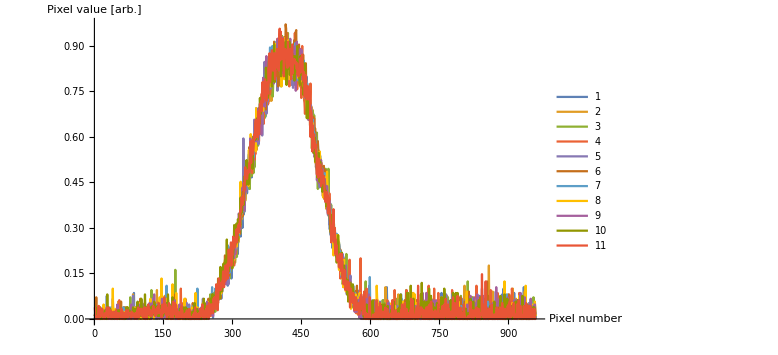

```mathematica
ListPlot[Evaluate[Table[linedata[j],{j,-5,5}]], Joined->True,AxesLabel-> {"Pixel number","Pixel value [arb.]"},LabelStyle-> Directive[Black, Medium],ImageSize-> Large,PlotRange->All,PlotLegends->Automatic]
```

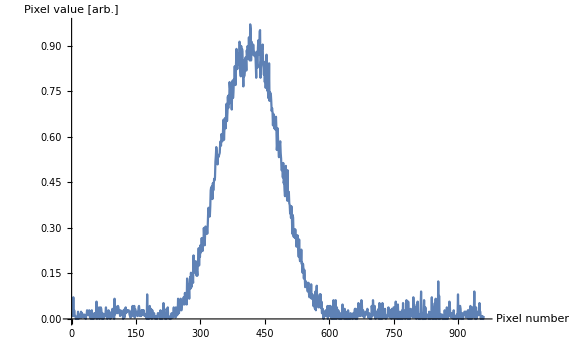

```mathematica
ListPlot[linedata[0], Joined->True,AxesLabel-> {"Pixel number","Pixel value [arb.]"},LabelStyle-> Directive[Black, Medium],ImageSize-> Large,PlotRange->All,PlotLegends->Automatic]
```

{μ→415.036,σ→137.707,A→0.909951}

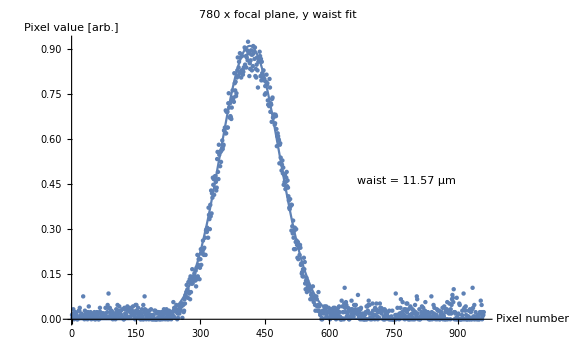

real space waist 11.57 [μm]

```mathematica
model = A  Exp[(-2(x-μ)^2)/σ^2];
fit =FindFit[linedata[0],model,{{μ,400},σ,A},x]
plt=Show[Plot[model/.fit,{x,0,lenx},PlotRange->All,PlotLegends-> Placed[ToString[StringForm["waist = `` μm",NumberForm[Values[fit[[2]]]/pixels780,4]]],{0.8,0.5}]],ListPlot[linedata[-5]],AxesLabel-> {"Pixel number","Pixel value [arb.]"},ImageSize-> Large,
PlotLabel->"780 x focal plane, y waist fit",LabelStyle-> Directive[Black, FontSize-> 14],ImageSize-> Medium]
StringForm["real space waist `` [μm]",NumberForm[Values[fit[[2]]]/pixels780,4]]
```

```mathematica
(*Export[ToString[FileNameJoin[{imagedir,"780_xfocus_ywaist_20210310.png"}]],plt]*)
```

C:\Users\gothr\Documents\Graduate Research\Mathematica\lab_analysis\FORT_MOT_images_20210309\780_xfocus_ywaist_20210310.png

show both slices:

```mathematica
beamslices=Show[Image[data],Graphics[{EdgeForm[Directive[Thin,Red]], Opacity[0],Rectangle[{620,1},{630,lenx}]}],Graphics[{EdgeForm[Directive[Thin,Red]], Opacity[0],Rectangle[{1,540},{leny,550}]}],ImageSize->Medium]
```

-Graphics-

```mathematica
Export[ToString[FileNameJoin[{imagedir,"780_beamslices_20210310.png"}]],beamslices]
```

C:\Users\gothr\Documents\Graduate Research\Mathematica\lab_analysis\FORT_MOT_images_20210309\780_beamslices_20210310.png

```mathematica
ToString[FileNameJoin[{imagedir,"780_beamslices_20210310.png"}]]
```

FileNameJoin[{FileNameJoin[{NotebookDirectory, FORT_MOT_images_20210309\}], 780_beamslices_20210310.png}]